```mathematica
Map[Length[#[[1]]]&,Map[SymbolToSets[FilterSymbol[#,{12,13,7,15,17}]]&,FindFullFormula4[ EmbedGraphInPlantri8[allGraphs5,lambdaKey]]]//Tally]
```

{4,4,3,4,3,3,4,3,4}

```mathematica
Table[Map[SymbolLevel[#]&,FindFullFormula4[ Graph[plantri[[k]]]]],{k,2}]
```

{{4,4,4,4,4,4,4,4,4,4},{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}}

```mathematica
Monitor[Table[
allGraphs5[k,"graph"]->{allGraphs5[k,"colofour"]/.RepGraph["C"],Sort[Map[Length[#[[1]]]&,Map[SymbolToSets[FilterSymbol[#,{12,13,7,15,17}]]&,FindFullFormula4[ EmbedGraphInPlantri8[allGraphs5,k]]]//Tally]]},
{k,Join[alfas,amigos,{lambdaKey,starKey}]}],allGraphs5[k,"graph"]]//Sort//TableForm
```

-Graphics-→{-Graphics-317380+-Graphics-317140+-Graphics-317110,{3,3,4}}
-Graphics-→{-Graphics-361660+-Graphics-361120+-Graphics-360850,{3,3,4}}
-Graphics-→{-Graphics-317140+-Graphics-296080+-Graphics-295270,{3,4}}
-Graphics-→{-Graphics-361660+-Graphics-296080+-Graphics-296050,{3,4}}
-Graphics-→{-Graphics-361120+-Graphics-317380+-Graphics-295510,{3,3,4}}
-Graphics-→{-Graphics-361660+-Graphics-361120+-Graphics-317380+-Graphics-317140+-Graphics-296080+-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295270+-Graphics-295240,{3,3,3,3,4,4,4,4,4}}
-Graphics-→{-Graphics-492161+-Graphics-492081+-Graphics-304961+-Graphics-297681+-Graphics-302621+-Graphics-492070+-Graphics-297670+-Graphics-295330+-Graphics-302530+-Graphics-295250+-Graphics-295240,{3,3,3,3,3,4,4,4,4,4}}
-Graphics-→{-Graphics-296080+-Graphics-296050+-Graphics-295510+-Graphics-295270+-Graphics-295240,{4,4,4}}
-Graphics-→{-Graphics-317380+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295240,{3,4,4,4}}
-Graphics-→{-Graphics-361120+-Graphics-360850+-Graphics-295510+-Graphics-295270+-Graphics-295240,{3,4,4,4}}
-Graphics-→{-Graphics-317140+-Graphics-360850+-Graphics-317110+-Graphics-295270+-Graphics-295240,{3,4,4,4}}
-Graphics-→{-Graphics-361660+-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295240,{3,4,4,4}}

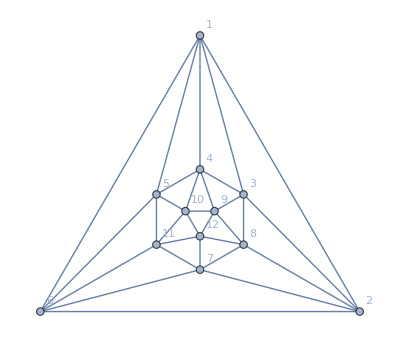

```mathematica
Graph[plantri[[1]],GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```

```mathematica
WorkonGraph[g_]:=Block[{centers,edges,h,vertices},
centers=Select[VertexList[g],VertexDegree[g,#]==5&];
PrintTemporary[centers];
Monitor[
Table[
edges=Select[EdgeList[g],#[[1]]==center||#[[2]]==center&];
vertices=Select[VertexList[Graph[edges]],#≠center&];
h=VertexDelete[g,center];
Sort[Tally[Map[With[{s=FilterSymbol[#,vertices]},{s,SymbolLevel[s]}]&,FindFullFormula4[ h]]],#1[[1,2]]>#2[[1,2]]&]
,{center,centers}
],
center]
]
```

```mathematica
Graph[plantri[[100]],GraphLayout->"TutteEmbedding",VertexLabels->"Name"]//VertexCount
```

20

```mathematica
t=WorkonGraph [Graph[plantri[[100]],GraphLayout->"TutteEmbedding",VertexLabels->"Name"]];
```

```mathematica
TableForm[t,TableDepth->2]
```

{{v18x3x7x9,4},12} | {{v19x3x7x8,4},20} | {{v1x3x79x8,4},11} | {{v1x37x8x9,4},22} | {{v1x38x7x9,4},19} | {{v18x37x9,3},22} | {{v18x3x79,3},11} | {{v19x37x8,3},30} | {{v19x38x7,3},27} | {{v1x38x79,3},18}
{{v1x35xdxe,4},22} | {{v1x3ex5xd,4},15} | {{v1dx3x5xe,4},24} | {{v1ex3x5xd,4},26} | {{v1x3x5dxe,4},17} | {{v1dx35xe,3},26} | {{v1ex35xd,3},28} | {{v1ex3x5d,3},23} | {{v1x3ex5d,3},12} | {{v1dx3ex5,3},19}
{{v1x46xexf,4},20} | {{v1x4x6exf,4},17} | {{v1fx4x6xe,4},22} | {{v1x4fx6xe,4},19} | {{v1ex4x6xf,4},26} | {{v1fx46xe,3},22} | {{v1ex46xf,3},26} | {{v1ex4fx6,3},25} | {{v1x4fx6e,3},16} | {{v1fx4x6e,3},19}
{{v1x5gx7xf,4},15} | {{v1x57xfxg,4},14} | {{v1gx5x7xf,4},32} | {{v1fx5x7xg,4},22} | {{v1x5x7fxg,4},11} | {{v1gx57xf,3},30} | {{v1gx5x7f,3},27} | {{v1x5gx7f,3},10} | {{v1fx57xg,3},20} | {{v1fx5gx7,3},21}
{{v18x2x6xg,4},12} | {{v1gx2x6x8,4},32} | {{v1x26x8xg,4},22} | {{v1x2gx6x8,4},27} | {{v1x2x68xg,4},11} | {{v18x26xg,3},14} | {{v18x2gx6,3},19} | {{v1gx2x68,3},23} | {{v1gx26x8,3},34} | {{v1x2gx68,3},18}
{{v2hx7x9xg,4},28} | {{v2x79xgxh,4},11} | {{v2x7hx9xg,4},20} | {{v2x7x9gxh,4},28} | {{v2gx7x9xh,4},27} | {{v2hx79xg,3},15} | {{v2hx7x9g,3},32} | {{v2x7hx9g,3},24} | {{v2gx79xh,3},14} | {{v2gx7hx9,3},23}
{{v2x3hx8xa,4},23} | {{v2hx3x8xa,4},28} | {{v2ax3x8xh,4},23} | {{v2x3x8axh,4},16} | {{v2x38xaxh,4},19} | {{v2x3hx8a,3},17} | {{v2hx38xa,3},25} | {{v2hx3x8a,3},22} | {{v2ax38xh,3},20} | {{v2ax3hx8,3},24}
{{v3x9xbhxi,4},16} | {{v3hx9xbxi,4},23} | {{v3x9bxhxi,4},16} | {{v3ix9xbxh,4},28} | {{v3x9ixbxh,4},11} | {{v3hx9ixb,3},18} | {{v3hx9bxi,3},23} | {{v3ix9xbh,3},28} | {{v3ix9bxh,3},28} | {{v3x9ixbh,3},11}
{{v3xajxcxi,4},28} | {{v3jxaxcxi,4},27} | {{v3xacxixj,4},20} | {{v3ixaxcxj,4},28} | {{v3xaxcixj,4},11} | {{v3xajxci,3},15} | {{v3ixajxc,3},32} | {{v3jxacxi,3},23} | {{v3ixacxj,3},24} | {{v3jxaxci,3},14}
{{v3xbdxjxk,4},11} | {{v3xbxdjxk,4},22} | {{v3jxbxdxk,4},27} | {{v3kxbxdxj,4},32} | {{v3xbkxdxj,4},12} | {{v3kxbxdj,3},34} | {{v3kxbdxj,3},23} | {{v3jxbkxd,3},19} | {{v3jxbdxk,3},18} | {{v3xbkxdj,3},14}
{{v3x4kxcxe,4},22} | {{v3x4cxexk,4},11} | {{v3x4xcexk,4},14} | {{v3ex4xcxk,4},15} | {{v3kx4xcxe,4},32} | {{v3kx4cxe,3},27} | {{v3x4kxce,3},20} | {{v3kx4xce,3},30} | {{v3ex4cxk,3},10} | {{v3ex4kxc,3},21}
{{v4x5kxdxf,4},26} | {{v4kx5xdxf,4},22} | {{v4x5xdfxk,4},20} | {{v4fx5xdxk,4},19} | {{v4x5dxfxk,4},17} | {{v4kx5dxf,3},19} | {{v4fx5kxd,3},25} | {{v4fx5dxk,3},16} | {{v4x5kxdf,3},26} | {{v4kx5xdf,3},22}
{{v5gx6xexk,4},15} | {{v5kx6xexg,4},26} | {{v5x6xegxk,4},22} | {{v5x6exgxk,4},17} | {{v5x6kxexg,4},24} | {{v5gx6kxe,3},19} | {{v5x6kxeg,3},26} | {{v5kx6xeg,3},28} | {{v5kx6exg,3},23} | {{v5gx6exk,3},12}
{{v8x9gxaxi,4},28} | {{v8ax9xgxi,4},16} | {{v8x9ixaxg,4},11} | {{v8ix9xaxg,4},16} | {{v8x9xagxi,4},23} | {{v8ax9ixg,3},11} | {{v8ix9gxa,3},28} | {{v8ax9gxi,3},28} | {{v8x9ixag,3},18} | {{v8ix9xag,3},23}
{{vaxbhxgxj,4},16} | {{vaxbxgxhj,4},23} | {{vajxbxgxh,4},28} | {{vaxbgxhxj,4},19} | {{vagxbxhxj,4},23} | {{vajxbgxh,3},25} | {{vajxbhxg,3},22} | {{vaxbgxhj,3},20} | {{vagxbhxj,3},17} | {{vagxbxhj,3},24}
{{vbgxcxixk,4},19} | {{vbxcgxixk,4},22} | {{vbxcixgxk,4},11} | {{vbkxcxgxi,4},12} | {{vbxcxgxik,4},20} | {{vbgxcixk,3},18} | {{vbgxcxik,3},27} | {{vbkxcixg,3},11} | {{vbxcgxik,3},30} | {{vbkxcgxi,3},22}

```mathematica
Map[#[[2]]&,t[[1]]]
```

```mathematica
Map[PartitionType[SymbolToSets[#]]&,FindFullFormula4[Graph[plantri[[1]]]]]//Tally
```

{{{3,3,3,3},10}}

```mathematica
WorkonGraph2[g_]:=Block[{centers,edges,h,vertices},
centers=Select[VertexList[g],VertexDegree[g,#]==5&];
PrintTemporary[centers];
Monitor[
Table[
edges=Select[EdgeList[g],#[[1]]==center||#[[2]]==center&];
vertices=Select[VertexList[Graph[edges]],#≠center&];
h=VertexDelete[g,center];
Map[PartitionType[SymbolToSets[#]]&,FindFullFormula4[h]]
,{center,centers}
],
center]
]
```

```mathematica
t=WorkonGraph2 [Graph[plantri[[10]],GraphLayout->"TutteEmbedding",VertexLabels->"Name"]];
```

```mathematica
TableForm[t,TableDepth->2]
```

{{5,5,4,2},2} | {{5,5,3,3},2} | {{4,4,4,4},34} | {{5,4,4,3},42}
{{5,5,4,2},2} | {{5,5,3,3},2} | {{4,4,4,4},34} | {{5,4,4,3},42}
{{5,5,4,2},10} | {{5,5,3,3},10} | {{4,4,4,4},30} | {{5,4,4,3},50}
{{5,5,4,2},2} | {{5,5,3,3},2} | {{4,4,4,4},34} | {{5,4,4,3},42}
{{5,5,3,3},2} | {{5,5,4,2},2} | {{4,4,4,4},34} | {{5,4,4,3},42}
{{5,5,4,2},2} | {{5,5,3,3},2} | {{4,4,4,4},34} | {{5,4,4,3},42}
{{5,5,4,2},2} | {{5,5,3,3},2} | {{4,4,4,4},34} | {{5,4,4,3},42}
{{5,5,3,3},2} | {{5,5,4,2},2} | {{4,4,4,4},34} | {{5,4,4,3},42}
{{5,5,4,2},2} | {{5,5,3,3},2} | {{4,4,4,4},34} | {{5,4,4,3},42}
{{5,5,3,3},10} | {{5,5,4,2},10} | {{4,4,4,4},30} | {{5,4,4,3},50}
{{5,5,4,2},2} | {{5,5,3,3},2} | {{4,4,4,4},34} | {{5,4,4,3},42}
{{5,5,4,2},2} | {{5,5,3,3},2} | {{4,4,4,4},34} | {{5,4,4,3},42}

```mathematica
t=WorkonGraph2 [Graph[plantri[[8]],GraphLayout->"TutteEmbedding",VertexLabels->"Name"]];
```

```mathematica
TableForm[t,TableDepth->2]
```

{{5,4,4,3},36} | {{4,4,4,4},32} |  | 
{{5,4,4,3},23} | {{4,4,4,4},40} |  | 
{{5,4,4,3},36} | {{4,4,4,4},32} |  | 
{{5,5,4,2},1} | {{5,5,3,3},1} | {{5,4,4,3},28} | {{4,4,4,4},38}
{{4,4,4,4},41} | {{5,4,4,3},22} |  | 
{{4,4,4,4},40} | {{5,4,4,3},23} |  | 
{{4,4,4,4},32} | {{5,4,4,3},36} |  | 
{{4,4,4,4},32} | {{5,4,4,3},36} |  | 
{{5,4,4,3},23} | {{4,4,4,4},40} |  | 
{{5,4,4,3},22} | {{4,4,4,4},41} |  | 
{{5,5,4,2},1} | {{5,5,3,3},1} | {{4,4,4,4},38} | {{5,4,4,3},28}
{{5,4,4,3},23} | {{4,4,4,4},40} |  |

```mathematica
t=WorkonGraph2 [Graph[plantri[[100]],GraphLayout->"TutteEmbedding",VertexLabels->"Name"]]
```

{{{5,5,5,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{6,5,4,4},{6,5,4,4},{6,5,4,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{6,5,4,4},{6,5,4,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},130,{5,5,5,4},{6,5,4,4},{5,5,5,4},{6,5,4,4},{6,5,4,4},{5,5,5,4},{6,5,4,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{6,5,4,4},{5,5,5,4},{5,5,5,4},{5,5,5,4},{6,5,5,3},{6,5,4,4},{6,5,4,4},{6,5,4,4},{6,5,5,3},{6,5,4,4},{6,5,4,4},{6,5,4,4},{5,5,5,4},{6,5,5,3},{6,5,4,4},{5,5,5,4},{6,5,5,3}},15}
 |  |  |  |

```mathematica
Sort[Tally[Flatten[t,1]]]
```

{{{5,5,5,4},2840},{{6,5,4,4},360},{{6,5,5,3},118},{{6,6,4,3},22},{{6,6,5,2},2}}

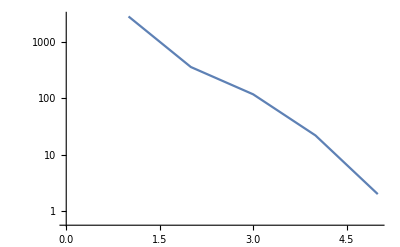

```mathematica
ListLogPlot[Map[Last,Sort[Tally[Flatten[t,1]]]],Joined->True]
```

```mathematica
Length[plantri]
```

100000

```mathematica
Monitor[TableForm[Table[k->Sort[Tally[Map[PartitionType[SymbolToSets[#]]&,FindFullFormula4[Graph[plantri[[k]]]]]]],{k,500}],TableDepth->2],k]
```

Tally::list: List expected at position 1 in Tally[1 → {{3, 3, 3, 3}, {3, 3, 3, 3}, {3, 3, 3, 3}, {3, 3, 3, 3}, {3, 3, 3, 3}, {3, 3, 3, 3}, {3, 3, 3, 3}, {3, 3, 3, 3}, {3, 3, 3, 3}, {3, 3, 3, 3}}].

Tally::list: List expected at position 1 in Tally[2 → {{4, 4, 4, 2}, {4, 4, 3, 3}, {4, 4, 3, 3}, {4, 4, 3, 3}, {4, 4, 3, 3}, {4, 4, 3, 3}, {4, 4, 3, 3}, {4, 4, 3, 3}, {4, 4, 3, 3}, {4, 4, 3, 3}, {4, 4, 3, 3}, {4, 4, 3, 3}, {4, 4, 3, 3}, {4, 4, 3, 3}, {4, 4, 3, 3}, {4, 4, 3, 3}, {4, 4, 3, 3}, {4, 4, 3, 3}, {4, 4, 3, 3}, {4, 4, 3, 3}}].

Tally::list: List expected at position 1 in Tally[3 → {{4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}, {4, 4, 4, 3}}].

General::stop: Further output of Tally :: list will be suppressed during this calculation.